```mathematica
DSolve[y'[x]==(x^2+3y[x]^2)/(2 x y[x]),y[x],x]/.C[1]->n
```

{{y[x]→-x √(-1+n x)},{y[x]→x √(-1+n x)}}

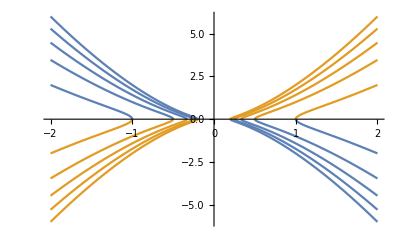

```mathematica
Plot[{Table[-x √(-1+n x),{n,-5,5}],Table[x √(-1+n x),{n,-5,5}]},{x,-2,2}]
```

```mathematica
Expand[-3(1-y/5)(1-y/9)y]
```

-3 y+(14 y^2)/15-y^3/15

```mathematica
fprime=D[%,y]
```

-3+(28 y)/15-y^2/5

```mathematica
Solve[fprime==0,y]
```

{{y→1/3 (14-√61)},{y→1/3 (14+√61)}}

```mathematica
Solve[15 fprime==0,y]
```

{{y→1/3 (14-√61)},{y→1/3 (14+√61)}}

```mathematica
15 fprime//Expand
```

-45+28 y-3 y^2